# Heaviside-Θ auf der komplexen Ebene

Dieses Worksheet soll eine spezielle Wahl einer analytischen Erweiterung der Heaviside-Funktion untersuchen, welche rechtfertigt, dass mein Integrationsverfahren auch mit großen Extradimensionen funktioniert. Dies tangiert im wesentlichen Appendix E.2 der Masterarbeit und wird im Haupttext nicht besprochen.

```mathematica
funk[k_,z_] = (1+Exp[-2k])/(1+Exp[-2k*z])
```

(1+ⅇ^(-2 k))/(1+ⅇ^(-2 k z))

## Übersichtsplots (Manipulates)

Hier erkennt man, dass die Funktion die Theta-Eigenschaft gut erfüllt auf dem reellen Zahlenstrahl.

```mathematica
Manipulate[
Plot[funk[k ,z],{z,-2,2}, PlotRange-> {-0.1,1.1}],
 {k, 0.05,20}]
```

Hier erkennt man, dass die Funktion wirklich die Theta-Eigenschaft gut erfüllt auf dem komplexen Einheitskreis:

```mathematica
Plot[Abs@funk[m, Exp[I φ]], {φ,0,2π},
GridLines-> {{π/2, π,3π/2, 2π},{1}}
]~Manipulate~{m,0.05,20}
```

Hier erkennt man, dass höhere Regularisierungswerte m zu immer besserer Theta-Auflösung führen.

```mathematica
Plot[Abs@funk[m, Exp[I φ]], {φ,0,π/2},
GridLines-> {{π/2, π,3π/2, 2π},{1}},
PlotRange-> 1+{-1,+1}/100
]~Manipulate~{m,0.05,20}
```

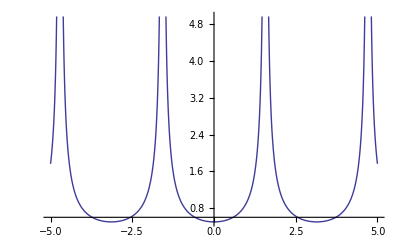

```mathematica
Plot[Abs@funk[I y], {y,-5,5},
GridLines-> {Table[n π/2,{n,-3,3}],{}}]
```

## Exportplots

## 3d-Plots

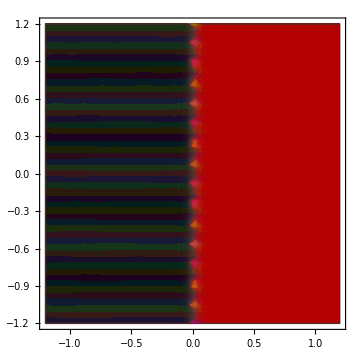

```mathematica
With[{fun = funk[19.5,#]&},ParametricPlot[
(*just need a vis function that will allow x and y to be in the color function*)
{x,y},{x,-1.2,1.2},{y,-1.2,1.2},
(*color and mesh functions don't trigger refinement,so just use a big grid*)
PlotPoints->50,MaxRecursion->0,Mesh->50,
PlotRangeClipping->False,(*turn off scaling so we can do computations with the actual complex values*)
ColorFunctionScaling->False,ColorFunction->(Hue[
(*hue according to argument,with shift so arg(z)==0 is red*)
Rescale[Arg[fun[#+I #2]],{-π,π},{0,1}+0.5],1,
(*fudge brightness a bit:
0.1 keeps things from getting too dark,
2 forces some actual bright areas*)
Rescale[Abs[fun[#+I #2]],{0,1.6},{0.21,1}]]&),
(*mesh lines according to magnitude,scaled to avoid the pole at z=1*)MeshFunctions->{Abs[fun[#1+I #2]]&},
Frame-> True,
ImageSize-> Medium,
PlotRange-> All,
FrameTicksStyle-> (FontOpacity-> 0.5),
BaseStyle->{FontSize->10} (* for export *)
]
]
```

```mathematica
With[{fun = funk[19.5,#]&},
Plot3D[Abs[fun[x+I y]],{x,-1,1},{y,-1,1},
(*color and mesh functions don't trigger refinement,so just use a big grid*)
PlotPoints->100,MaxRecursion->0,Mesh->100,
(*turn off scaling so we can do computations with the actual complex values*)
ColorFunctionScaling->False,ColorFunction->(Hue[
(*hue according to argument,with shift so arg(z)==0 is red*)
Rescale[Arg[fun[#+I #2]],{-π,π},{0,1}+0.5],1,(*fudge brightness a bit:0.1 keeps things from getting too dark,2 forces some actual bright areas*)Rescale[Log[Abs[fun[#+I #2]]],{-2,2},{0.1,2}]]&),
(*mesh lines according to magnitude,scaled to avoid the pole at z=1*)MeshFunctions->{Log[Abs[fun[#1+I #2]]]&},
AxesLabel->{Re, Im, Abs},
PlotLabel-> "Abs value from function",
PlotRange-> {0,4},
BaseStyle->{FontSize->10} (* for export *)
]
]
```

-Graphics3D-